```mathematica
Vmorse[a_,re_,De_,r_]:=De (1-ⅇ^(-(r-re)/a))^2-De
```

```mathematica
Vdiag[r_,a_,re_,D11_,D22_,D33_,Eth_]:=({{Vmorse[a,re,D11,r]+Eth[[1]], 0, 0}, {0, Vmorse[a,re,D22,r]+Eth[[2]], 0}, {0, 0, Vmorse[a,re,D33,r]+Eth[[3]]}});
Vcoupling[r_,a_,V12_,V23_,r12_,r23_,a12_,a23_]:=({{0, V12 ⅇ^(-(r-r12)^2/a12^2), 0}, {V12 ⅇ^(-(r-r12)^2/a12^2), 0, V23 ⅇ^(-(r-r23)^2/a23^2)}, {0, V23 ⅇ^(-(r-r23)^2/a23^2), 0}});
```

```mathematica
Vmat[r_,a_,re_,D11_,D22_,D33_,V12_,V23_,r12_,r23_,a12_,a23_,Eth_]:=Vdiag[r,a,re,D11,D22,D33,Eth]+Vcoupling[r,a,V12,V23,r12,r23,a12,a23]
```

```mathematica
Nchan=3;
Eth={0.0,3.0,5.0};
a=1;
re=1;
l=0;
rmin=0.0;
rmax=12.0;
D11=1.0;
D22=4.0;
D33=6.0;
V12=0.2;
V23=0.2;
r12=0.5;
r23=1.0;
a12=0.5;
a23=0.5;
```

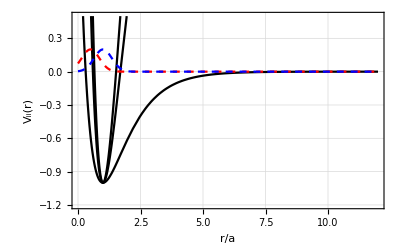

```mathematica
vcscale=1;Clear[VV];VV[r_]=Vmat[r,a,re,D11,D22,D33,V12,V23,r12,r23,a12,a23,Eth];Plot[{Diagonal[VV[r]],vcscale VV[r][[1,2]],vcscale VV[r][[2,3]]},{r,rmin,rmax},Frame->True,GridLines->Automatic,PlotStyle->{{Black},{Red,Dashed},{Blue,Dashed}},LabelStyle->Large,FrameLabel->{"r/a","V_ii(r)"},PlotRange->{-1.2,0.5}]
```

```mathematica
VV[0.1]
```

{{1.13044,0.105458,0},{0.105458,7.52176,0.00783278},{0,0.00783278,11.7826}}

```mathematica
Clear[umat,u];
umat=Table[Subscript[u, i,j],{i,1,Nchan},{j,Nchan}];
```

```mathematica
boundarycondBOUND=Table[{
umat[[i,α]][rmin]==0,
umat[[i,α]][rmax]==0
},{i,1,Nchan},{α,1,Nchan}]
```

{{{u_(1,1)[0]==0,u_(1,1)[20]==0},{u_(1,2)[0]==0,u_(1,2)[20]==0},{u_(1,3)[0]==0,u_(1,3)[20]==0}},{{u_(2,1)[0]==0,u_(2,1)[20]==0},{u_(2,2)[0]==0,u_(2,2)[20]==0},{u_(2,3)[0]==0,u_(2,3)[20]==0}},{{u_(3,1)[0]==0,u_(3,1)[20]==0},{u_(3,2)[0]==0,u_(3,2)[20]==0},{u_(3,3)[0]==0,u_(3,3)[20]==0}}}

```mathematica
MatrixForm[umat[[1]]]
```

(u_(1,1)
u_(1,2)
u_(1,3))

```mathematica
eqs[r_,Ε_]:=Table[-Laplacian[umat[[i,α]][r],{r}]+Sum[(VV[r][[i,j]])umat[[j,α]][r],{j,1,Nchan}],{i,1,Nchan},{α,1,Nchan}];
```

```mathematica
alleqsBOUND[r_,Ε_]:=Table[Flatten[{Transpose[eqs[r,Ε]][[α]],Transpose[boundarycondBOUND][[α]]}],{α,1,Nchan}]
```

```mathematica
alleqsBOUND[r,Ε]
```

{{(-1.+1. (1-ⅇ^(1-r))^2) u_(1,1)[r]+0.2 ⅇ^(-4. (-0.5+r)^2) u_(2,1)[r]-u_(1,1)''[r],0.2 ⅇ^(-4. (-0.5+r)^2) u_(1,1)[r]+(-1.+4. (1-ⅇ^(1-r))^2) u_(2,1)[r]+0.2 ⅇ^(-4. (-1.+r)^2) u_(3,1)[r]-u_(2,1)''[r],0.2 ⅇ^(-4. (-1.+r)^2) u_(2,1)[r]+(-1.+6. (1-ⅇ^(1-r))^2) u_(3,1)[r]-u_(3,1)''[r],u_(1,1)[0]==0,u_(1,1)[20]==0,u_(2,1)[0]==0,u_(2,1)[20]==0,u_(3,1)[0]==0,u_(3,1)[20]==0},{(-1.+1. (1-ⅇ^(1-r))^2) u_(1,2)[r]+0.2 ⅇ^(-4. (-0.5+r)^2) u_(2,2)[r]-u_(1,2)''[r],0.2 ⅇ^(-4. (-0.5+r)^2) u_(1,2)[r]+(-1.+4. (1-ⅇ^(1-r))^2) u_(2,2)[r]+0.2 ⅇ^(-4. (-1.+r)^2) u_(3,2)[r]-u_(2,2)''[r],0.2 ⅇ^(-4. (-1.+r)^2) u_(2,2)[r]+(-1.+6. (1-ⅇ^(1-r))^2) u_(3,2)[r]-u_(3,2)''[r],u_(1,2)[0]==0,u_(1,2)[20]==0,u_(2,2)[0]==0,u_(2,2)[20]==0,u_(3,2)[0]==0,u_(3,2)[20]==0},{(-1.+1. (1-ⅇ^(1-r))^2) u_(1,3)[r]+0.2 ⅇ^(-4. (-0.5+r)^2) u_(2,3)[r]-u_(1,3)''[r],0.2 ⅇ^(-4. (-0.5+r)^2) u_(1,3)[r]+(-1.+4. (1-ⅇ^(1-r))^2) u_(2,3)[r]+0.2 ⅇ^(-4. (-1.+r)^2) u_(3,3)[r]-u_(2,3)''[r],0.2 ⅇ^(-4. (-1.+r)^2) u_(2,3)[r]+(-1.+6. (1-ⅇ^(1-r))^2) u_(3,3)[r]-u_(3,3)''[r],u_(1,3)[0]==0,u_(1,3)[20]==0,u_(2,3)[0]==0,u_(2,3)[20]==0,u_(3,3)[0]==0,u_(3,3)[20]==0}}

```mathematica
μ=1/2;De=4;a=1;re=1;
l=0;rmin=0;rmax=20;
NDEigensystem[alleqsBOUND[r,Ε],Flatten[umat],{r,rmin,rmax},3,Method->{"SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.2}}}]
```

NDEigensystem[{{(-1.+1. (1-ⅇ^(1-r))^2) u_(1,1)[r]+0.2 ⅇ^(-4. (-0.5+r)^2) u_(2,1)[r]-u_(1,1)''[r],0.2 ⅇ^(-4. (-0.5+r)^2) u_(1,1)[r]+(-1.+4. (1-ⅇ^(1-r))^2) u_(2,1)[r]+0.2 ⅇ^(-4. (-1.+r)^2) u_(3,1)[r]-u_(2,1)''[r],0.2 ⅇ^(-4. (-1.+r)^2) u_(2,1)[r]+(-1.+6. (1-ⅇ^(1-r))^2) u_(3,1)[r]-u_(3,1)''[r],u_(1,1)[0]==0,u_(1,1)[20]==0,u_(2,1)[0]==0,u_(2,1)[20]==0,u_(3,1)[0]==0,u_(3,1)[20]==0},{(-1.+1. (1-ⅇ^(1-r))^2) u_(1,2)[r]+0.2 ⅇ^(-4. (-0.5+r)^2) u_(2,2)[r]-u_(1,2)''[r],0.2 ⅇ^(-4. (-0.5+r)^2) u_(1,2)[r]+(-1.+4. (1-ⅇ^(1-r))^2) u_(2,2)[r]+0.2 ⅇ^(-4. (-1.+r)^2) u_(3,2)[r]-u_(2,2)''[r],0.2 ⅇ^(-4. (-1.+r)^2) u_(2,2)[r]+(-1.+6. (1-ⅇ^(1-r))^2) u_(3,2)[r]-u_(3,2)''[r],u_(1,2)[0]==0,u_(1,2)[20]==0,u_(2,2)[0]==0,u_(2,2)[20]==0,u_(3,2)[0]==0,u_(3,2)[20]==0},{(-1.+1. (1-ⅇ^(1-r))^2) u_(1,3)[r]+0.2 ⅇ^(-4. (-0.5+r)^2) u_(2,3)[r]-u_(1,3)''[r],0.2 ⅇ^(-4. (-0.5+r)^2) u_(1,3)[r]+(-1.+4. (1-ⅇ^(1-r))^2) u_(2,3)[r]+0.2 ⅇ^(-4. (-1.+r)^2) u_(3,3)[r]-u_(2,3)''[r],0.2 ⅇ^(-4. (-1.+r)^2) u_(2,3)[r]+(-1.+6. (1-ⅇ^(1-r))^2) u_(3,3)[r]-u_(3,3)''[r],u_(1,3)[0]==0,u_(1,3)[20]==0,u_(2,3)[0]==0,u_(2,3)[20]==0,u_(3,3)[0]==0,u_(3,3)[20]==0}},{u_(1,1),u_(1,2),u_(1,3),u_(2,1),u_(2,2),u_(2,3),u_(3,1),u_(3,2),u_(3,3)},{r,0,20},3,Method→{SpatialDiscretization→{FiniteElement,MeshOptions→{MaxCellMeasure→0.2}}}]

```mathematica
{vals,funs}=NDEigensystem[alleqsBOUND[r,Ε],u[r],{r,rmin,rmax},3,Method->{"SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.2}}}];
```